```mathematica
h[y_] = H Exp[(2y)/L]
DSolve[ (f D[h[y], y])/h[y]^2 F[y] + c D[F'[y]/h[y],y] == 0, F[y], y]
```

ⅇ^((2 y)/L) H

{{F[y]→ⅇ^(((c-√(c^2-2 c f L)) y)/(c L)) C[1]+ⅇ^(((c+√(c^2-2 c f L)) y)/(c L)) C[2]}}

```mathematica
D[F'[y]/(α y),y]
```

-F'[y]/(y^2 α)+F''[y]/(y α)

```mathematica
h[y_] = α y
DSolve[ (f D[h[y], y])/h[y]^2 F[y] + c D[F'[y]/h[y],y] == 0, F[y], y]
```

y α

{{F[y]→(2 f y BesselJ[2,(2 √f √y)/(√c)] C[1])/c-(2 f y BesselY[2,(2 √f √y)/(√c)] C[2])/c}}

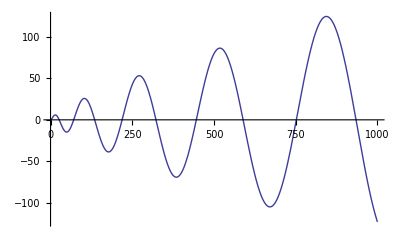

```mathematica
Plot[ y BesselJ[2, Sqrt[y]], {y, 0, 1000}]
```

```mathematica
Limit[y BesselK[2, Sqrt[y]], y-> 0, Direction-> -1]
```

2

```mathematica
D[y/Rd BesselJ[2, Sqrt[y/Rd]], y]
```

BesselJ[2,√(y/Rd)]/Rd+(y (BesselJ[1,√(y/Rd)]-BesselJ[3,√(y/Rd)]))/(4 Rd^2 √(y/Rd))

```mathematica
Plot[D[y BesselJ[2, Sqrt[y]]], {y, 0, 1000}]
```

Plot::exclul: {Im[y/Rd] - 0} must be a list of equalities or real-valued functions.

-Graphics-